```mathematica
Clear["Global`*"];
```

```mathematica
V[p_]=Gamma[-Y]((M-p)^Y-M^Y);
```

```mathematica
M=2;Y=3/2;Gamma[-Y];
```

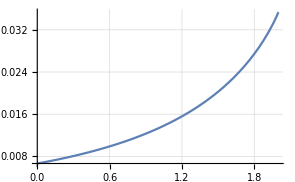

```mathematica
Plot[Exp[V[p]/p],{p,0,M},GridLines->Automatic]
```

```mathematica
f[x_]=Exp[M x];f''[x]
```

ⅇ^(M x) M^2

```mathematica
"1/2 M^2 Exp[M ξ]";
```

```mathematica
λ=1+Y;β=1;α=M;Simplify[Series[1/(1-z)^λ,{z,0,4}]]
```

1+(1+Y) z+1/2 (1+Y) (2+Y) z^2+1/6 (1+Y) (2+Y) (3+Y) z^3+1/24 (1+Y) (2+Y) (3+Y) (4+Y) z^4+O[z]^5

```mathematica
ρ[n_]=M+n-1;ρhat[n_]=-G-(n-1);
```

```mathematica
"z=Exp[-M x]";
```

```mathematica
λ=1+Y;β=1;α=M;
```

```mathematica
ν[x_]=ⅇ^(-M x) (1-ⅇ^-x)^(-1-Y)HeavisideTheta[x]+ⅇ^(-G Abs[x]) (1-ⅇ^(-Abs[x]))^(-1-Y)HeavisideTheta[-x];
```

```mathematica
"φ2[z_]=NIntegrate[(Exp[z x]-1-z x)ν[x],{x,-Infinity,Infinity},WorkingPrecision→30,MaxRecursion→20]";
```

```mathematica
B[x_,y_]=Gamma[x]Gamma[y]/Gamma[x+y];
```

```mathematica
φ[z_]=1/β(B[α-z/β,1-λ]-B[α,1-λ])+1/β2(B[α2+z/β2,1-λ2]-B[α2,1-λ2]);
```

```mathematica
λ=1+Y;β=1;α=M;λ2=1+Y;β2=1;α2=G;
```

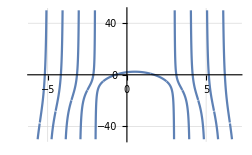

```mathematica
Y=3/2;M=3;G=2;q=2;Plot[q-φ[z],{z,-G-4,M+4},GridLines->Automatic,PlotRange->{-50,50}]
```

```mathematica
z=5/2;N[φ[z]]
```

7.0778

```mathematica
b=-1.5451774444795624317922257659001298180072385971486634642242`30.;b z+NIntegrate[(Exp[z x]-1-z x)ν[x],{x,-20,20},WorkingPrecision->30,MaxRecursion->20]
```

7.0777103929289978236453525558

```mathematica
Clear[z];Quiet[Plot[b z+NIntegrate[(Exp[z x]-1-z x)ν[x],{x,-1,1},WorkingPrecision->30,MaxRecursion->20],{z,0,M-.1},PlotPoints->10]]
```

$Aborted

```mathematica
Clear[z];
```

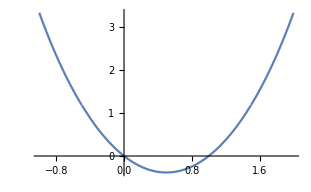

```mathematica
Plot[φ[z],{z,-G+1,M-1}]
```

```mathematica
ϵ=10^(-4);ξ[1]=z/.FindRoot[q-φ[z],{z,ϵ,M-ϵ}]
```

1.72089

```mathematica
ξhat[1]=-z/.FindRoot[q-φ[z],{z,-G+ϵ,-ϵ}]
```

0.720893

```mathematica
"q-φ[-ξhat[1]]";
```

```mathematica
N1=50;For[i=2,i≤N1,i++,ξ[i]=z/.FindRoot[q-φ[z],{z,M+(i-2)+ϵ,M+i-1-ϵ}];
ξhat[i]=-z/.FindRoot[q-φ[z],{z,-G-1-(i-2)+ϵ,-G-ϵ-(i-2)}];
]
```

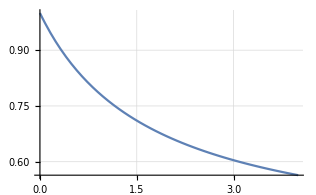

```mathematica
Plot[Product[(1+z/ρ[n])/(1+z/ξ[n]),{n,1,M}],{z,0,4},GridLines->Automatic]
```

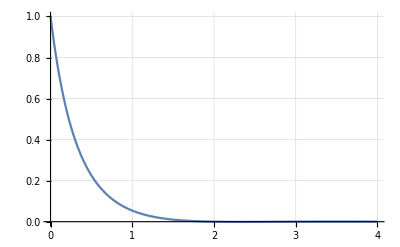

```mathematica
Plot[Product[(1+z/ρhat[n])/(1+z/ξhat[n]),{n,1,M}],{z,0,4},GridLines->Automatic,PlotRange->All]
```

```mathematica
ρhat[1]
```

-2

```mathematica
ρhat[2]
```

-3